```mathematica
(* https://mathematica.stackexchange.com/questions/261561/generating-1-f-noise *)
(* Timmer Konig 1995 *)
(* astrochron/R/FUNCTION-makeNoise_v3.R *)
```

```mathematica
nn=2^22(*Number of spectral points*)
S[f_]:=1/f;
Timing[
s1=Table[If[f!=nn/2,
(RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]]),
RandomVariate[NormalDistribution[]]]*
 Sqrt[S[f]/2],{f,1,nn/2 }];
s2=Join[{0},s1,Reverse[Conjugate[s1[[1;;-2]]]]];
]
pwr=s2.Conjugate[s2];
norm=1/Sqrt[pwr];
```

4194304

{22.9337,Null}

{0.16154,Null}

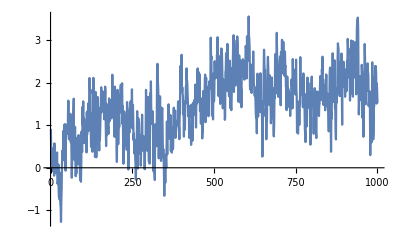

```mathematica
Timing[if=InverseFourier[s2,FourierParameters->{-1,-1}];]
l=Chop[norm if];
ListLinePlot[Take[l,UpTo[1000]]]
```

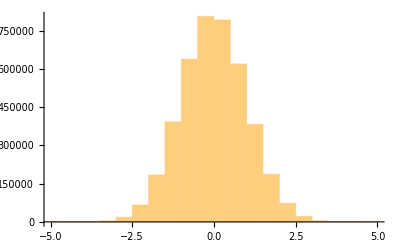

9.71445×10^-17

1.

```mathematica
Histogram[l]
avg=Mean[l]
std=StandardDeviation[l]
```

{{0,1.},{1,0.891663},{2,0.839796},{3,0.815398},{4,0.795342},{5,0.781333},{6,0.768765},{7,0.758775},{8,0.749784},{9,0.7421},{10,0.73487},{11,0.728695},{12,0.722897},{13,0.717659},{14,0.712578},{15,0.708123},{16,0.703906},{17,0.699773},{18,0.695787},{19,0.692237},{20,0.688808},{21,0.685652},{22,0.682593},{23,0.679787},{24,0.677041},{25,0.674402},{26,0.671802},{27,0.669187},{28,0.666675},{29,0.664247},{30,0.661838},{31,0.659618},{32,0.657577},{33,0.655645},{34,0.653448},{35,0.651539},{36,0.649642},{37,0.647797},{38,0.646108},{39,0.644413},{40,0.642818},{41,0.641181},{42,0.639381},{43,0.637816},{44,0.636654},{45,0.635143},{46,0.633631},{47,0.632259},{48,0.630956},{49,0.629618},{50,0.628114},{51,0.626709},{52,0.625335},{53,0.623995},{54,0.622742},{55,0.621575},{56,0.620349},{57,0.619152},{58,0.61796},{59,0.616873},{60,0.615822},{61,0.614658},{62,0.613651},{63,0.612731},{64,0.611854},{65,0.610867},{66,0.610091},{67,0.609301},{68,0.608467},{69,0.607516},{70,0.606744},{71,0.60582},{72,0.604876},{73,0.603989},{74,0.603016},{75,0.602139},{76,0.601234},{77,0.600438},{78,0.599736},{79,0.598913},{80,0.598121},{81,0.597349},{82,0.596532},{83,0.59556},{84,0.594694},{85,0.593935},{86,0.593207},{87,0.592289},{88,0.591641},{89,0.591002},{90,0.590306},{91,0.589528},{92,0.588893},{93,0.588164},{94,0.587478},{95,0.586601},{96,0.585846},{97,0.585141},{98,0.584386},{99,0.583649},{100,0.582967}}

{a→0.887412,b→0.0661807}

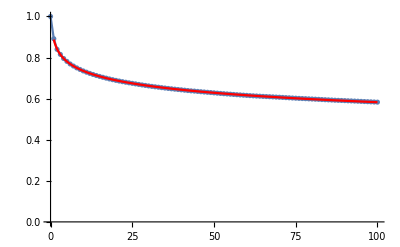

```mathematica
cf=Table[{i,CorrelationFunction[l-avg,i]},{i,0,100}]
p1=ListPlot[cf,PlotRange->{0,1},Joined->True,Mesh->All];
fnc=a-b Log[t];
sol=FindFit[Drop[cf,1],fnc,{a,b},t]
fnc=fnc/.sol;
p2=Plot[fnc,{t,1,100},PlotStyle->Red];
Show[p1,p2]
(* Logarithmic autocorrelation, see Kechner 1982 *)
```

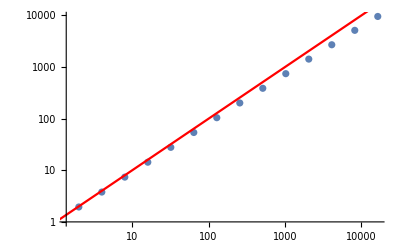

```mathematica
tab=Table[{2^i,StandardDeviation[Map[Total,Partition[l,2^i]]]},{i,14}];
p1=ListLogLogPlot[tab];
p2=LogLogPlot[{1x^(1)},{x,1,Length[l]},PlotStyle->{Red}];
Show[p1,p2]
```

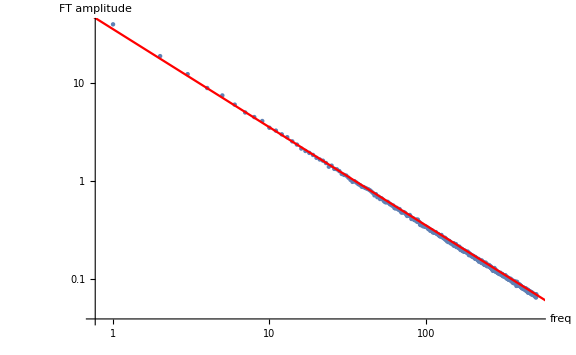

```mathematica
sz=1024;
pl=Partition[l,sz];
(* power spectrum ! *)
pl=Map[(μ=Mean[#];Rest[Take[Abs[Fourier[#-μ]]^2,sz/2]])&,pl];
plavg=Mean[pl];
pft1=ListLogLogPlot[plavg,PlotRange->All,AxesLabel->{"freq","FT amplitude"},LabelStyle->Larger];
pft2=LogLogPlot[{35/ω},{ω,0.1,10^6},PlotStyle->{Red}];
Show[pft1,pft2,ImageSize->8 72]
```